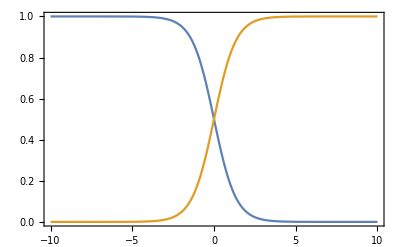

```mathematica
xmale [x_]:=1/(1+Exp[1.5x]);
xvelke[x_]:= 1/(1+Exp[-1.5x]);
Plot[{xmale[x],xvelke[x]}, {x, -10, 10}, 
Frame->{True, True, False, False}, 
Axes-> False,
PlotRange->{{-10,10}, {0,1}}]
```

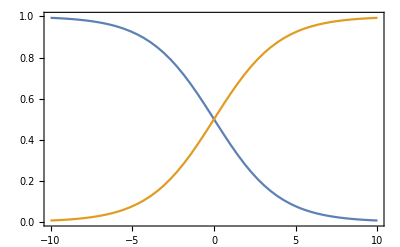

```mathematica
ymale [x_]:=1/(1+Exp[0.5x]);
yvelke[x_]:= 1/(1+Exp[-0.5x]);
Plot[{ymale[x],yvelke[x]}, {x, -10, 10}, 
Frame->{True, True, False, False}, 
Axes-> False,
PlotRange->{{-10,10}, {0,1}}]
```

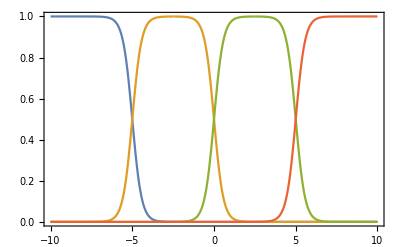

```mathematica
wa[x_]:=1/(1+Exp[3.5(x+5)]);
wb[x_]:=Min[1/(1+Exp[-3.5(x+5)]),1/(1+Exp[3.5x])];
wc[x_]:=Min[1/(1+Exp[-3.5x]),1/(1+Exp[3.5(x-5)])];
wd[x_]:=1/(1+Exp[-3.5(x-5)]);
Plot[{wa[x],wb[x],wc[x],wd[x]}, {x, -10, 10}, 
Frame->{True, True, False, False}, 
Axes-> False,
PlotRange->{{-10,10}, {0,1}}]
```

```mathematica
z={};
For[x=-10,x≤10,x+=1, 
For[y=-10, y≤10, y+=1,
total = 0;
totalp=0;
For[w=-10,w≤10,w+=1,
temp=Max[Min[xmale[x],ymale[y],wa[w]],
		Min[xmale[x],yvelke[y], wb[w]],
		Min[xvelke[x],ymale[y], wc[w]],
		Min[xvelke[x],yvelke[y], wd[w]]];
total += temp*w;
totalp+= temp;];
z=Append[z, {x,y,total/totalp}]
]
];
ListPlot3D[z, ColorFunction->"TemperatureMap"]
```

-Graphics3D-